# 量子算法：QFT与Shor算法

## Quantum Fourier Transformation and Shor’s Algorithm

## 魏文杰

## 癸卯年十月廿一2023年12月3日13:19:02

```mathematica
<<Wolfram`QuantumFramework`
```

## 目录

量子算法预备

Deutsch算法

量子傅里叶变换

QFT的应用：相位估计

大数分解与Shor算法

Fourier变换的一般应用

总结：需要记住的关键知识点

参考文献和注释

## 量子算法预备

### 量子算法的应用清单1：应用领域2

凝聚态、核物理、高能物理、量子化学、组合(又称，离散)优化、连续优化、密码学与密码分析、微分方程、金融、经典数据的机器学习

### 重点介绍的两种量子算法

基于量子傅里叶变换QFT的算法

相位估计 phase estimation

1994 Shor算法，多项式时间的因数分解算法。因数分解 ∈ BQP

离散对数问题 discrete log

隐藏子群问题 hidden subgroup

QFT

quantum field theory

quantum fluctuation theorem

quantum Fourier transformation

quantum fault tolerance

量子搜索算法

1996  Grover 算法对非结构化搜索问题进行了量子二次加速

推广：振幅放大 amplitude amplification

量子计算机要想对精确组合优化产生影响，必须做到以下两点之一：1）量子硬件的预期底层时钟速度和容错量子计算的开销取得巨大进步；或2）量子算法的开发大大超过Grover算法提供的四倍速度3。

### 其他量子算法

参见：量子算法动物园 以及综述 4

连续优化问题的相关算法：纳什均衡与线性规划问题

变分量子求解器 Variational Quantum Eigensolver

量子随机游走

1985 黑箱(oracle)算法：Deutsch 算法

更多黑箱算法：Deutsch-Jozsa、Bernstein-Vazirani和Simon算法

量子通信协议：1984 Charles Bennett 和 Gilles Brassard 将量子理论应用于密码协议，并证明量子密钥分发(QKD)可以增强信息安全性

2023新纪录：千公里以上的QKD

量子模拟算法

1980s Richard Feynman：在量子计算机上模拟量子系统

1996  Seth Lloyd ：以小时间步长演化可以有效模拟任何包含少粒子相互作用的多体量子哈密顿量； 模拟所需的总时间呈多项式增长。另一个链接

新世代的攻防战：后(抗)量子加密 post-quantum cryptography

量子计算的威力：
BQP是否严格大于BPP？但愿存在某些问题是量子计算机的概率算法能高效解决，但是概率图灵机不能高效解决的
大规模的容错量子计算能否实现？

## Deutsch算法

### 量子并行：Deutsch 算法

黑箱问题：给定黑箱函数 f : {0,1}{0,1}，判断 f 是平衡型还是常数型

量子并行：量子计算机能同时（在同一个幺正变换中）计算函数f(x)在许多x处的值

#### 平衡型函数 f (x) = x 或者 f(x)=x1

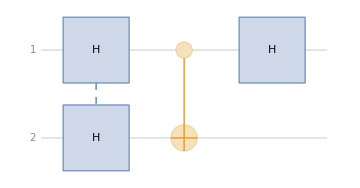

```mathematica
qc1 = QuantumCircuitOperator[{"H"->{1,2},"CNOT","H"}];(*设f(x) = x*)
qc1["Diagram"]
QuantumCircuitMultiwayGraph[qc1];
```

```mathematica
steps=ComposeList[qc1["Operators"],QuantumState[{0,1,0,0}]];
```

```mathematica
Grid[Transpose[{Style[#,Bold]&/@{"初态","经过前两个H门","(:7ecf:8fc7U)_f","经过最后的H门"},#["Formula"]&/@steps⟦;;⟧}],Frame->All,Alignment->Left]
```

初态 | 01
经过前两个H门 | 1/2 00-1/201+1/2 10-1/211
经过U_f | 1/2 00-1/201-1/210+1/2 11
经过最后的H门 | 1/(√2)10-1/(√2)11

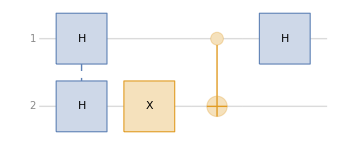

-1/(√2)10+1/(√2)11

```mathematica
qc2 = QuantumCircuitOperator[{"H"->{1,2},"X"->2,"CNOT","H"}];(*f(x)=x1*)
qc2["Diagram"]
qc2[QuantumState[{0,1,0,0}]]["Formula"]
```

#### 常数型函数 f(x)=1或 f(x)=0

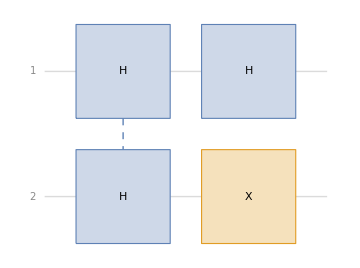

-1/(√2)00+1/(√2)01

```mathematica
qc3 = QuantumCircuitOperator[{"H"->{1,2},"X"->2,"H"}];(*f(x)=1*)
qc3["Diagram"]
qc3[QuantumState[{0,1,0,0}]]["Formula"]
```

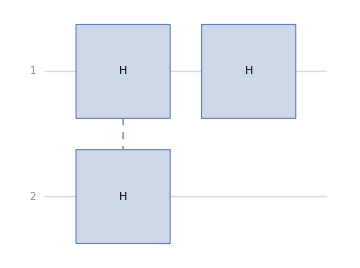

1/(√2)00-1/(√2)01

```mathematica
qc4 = QuantumCircuitOperator[{"H"->{1,2},"H"}];(*f(x)=1*)
qc4["Diagram"]
qc4[QuantumState[{0,1,0,0}]]["Formula"]
```

根据第一个qubit的测量结果，我们就能知道函数是平衡型还是常数型，也即计算了f(0)f(1)的值，对于常数型f(0)f(1)=0，对于平衡型f(0)f(1)=1

每个量子线路都只使用了一次U_f，即只需要一次计算就完成了经典计算需要两次计算才能完成的任务

启发：对于那些经典计算获得的信息量超过问题的答案能够提供的信息量的问题（尝试计算信息量），也即经典计算存在计算冗余的问题，量子计算具有潜在的加速可能

判断平衡型和常数型的量子算法推广到 f 具有 n 个slot的情况，称为Deutsch-Jozsa算法，参见 Sec.1.4.4

### Deutsch-Jozsa算法

## 量子傅里叶变换

### 经典的离散傅里叶变换

傅里叶分析、调和分析：由基本波的叠加来表示其他函数或是信号

1/(√N)∑_(r=1)^N u_r e^(2π i(r-1)(s-1)/N) , s =1 , ... , N

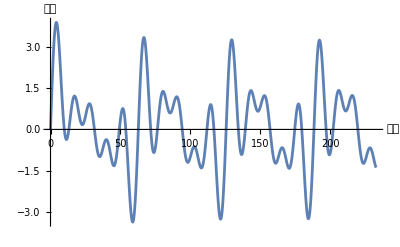

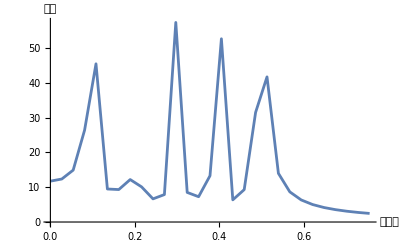

```mathematica
Clear[f];
num=13400;(*总采样点数*)
timespan=233;(*采样持续时间*)
bandwidth=num/(2timespan);(*采样率、带宽(实际上是不同的概念)*)
f[t_]:=(Sin[0.1 t]+E^(-0.03 t)Sin[0.2t]+Sin[0.3t]+Sin[0.4t]+Sin[0.5t]);
mat2=Table[f[timespan*i/num],{i,0,num}];
ListLinePlot[Table[{timespan*i/num,f[timespan*i/num]},{i,0,num}],AxesLabel->{"时间","振幅"}]
four=Abs@Fourier@mat2;
da=Table[{(k*2*Pi)/timespan,four[[k+1]]},{k,0,bandwidth}];
ListLinePlot[da,PlotRange->All,AxesLabel->{"角频率","振幅"}]
```

### 量子Fourier变换

1/(√N)∑_(k=0)^(N-1) e^(2π i j k/N)u_k , j =0, ... , N-1

注意Fourier变换是线性变换，因此才有显然的量子类比

计算基的态 取代了数列的项  ，j_i 取零或一

约定：低位比特在线路图中靠上，在bracket中靠左，即，越靠上或越靠左的比特的索引序号越小。(这种约定导致做加法时向低位进位，01+01=10)

序列的长度为 N，至少需要多少比特？1+ log_2 N

写成大家喜闻乐见的bracket算符形式和矩阵形式

-Graphics-

-Graphics--Graphics-

特殊的范德蒙德矩阵，只要设 -Graphics-

-Graphics-

因式分解

-Graphics-

作为上式的推论，计算基中的态Fourier变换后是直积态。

上式右边的因式分解能帮助我们利用简单的门逻辑门设计 Fourier 变换线路。

证明

-Graphics-

最后一行可以利用指数函数的周期性进行化简，定义二进制数的小数部分

上述算法被称为快速傅里叶变换FFT

Fourier 变换的结果被储存在概率幅中，无法直接读取，只能用统计方法推断，需要用更加巧妙的方法加以利用。

检验QFT的幺正性

```mathematica
Block[{n,m},n=3;m=1/(√2)^n(VandermondeMatrix[Table[o^k,{k,1,2^n}]]//Normal)/.o->E^(I (2π)/2^n)//N;
(m//Inverse//N//Chop)==ConjugateTranspose[m]]
```

True

### 量子线路

两比特 N = 4 ,n = 2

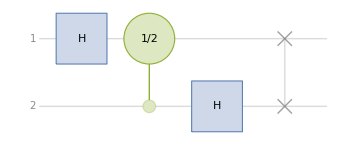

(1/2 | 1/2 | 1/2 | 1/2
1/2 | ⅈ/2 | -1/2 | -ⅈ/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | -ⅈ/2 | -1/2 | ⅈ/2)

```mathematica
qft2=QuantumCircuitOperator["Fourier"];
%//TraditionalForm
qft2["Matrix"]//Normal//MatrixForm
```

```mathematica
qft2["Operators"][[2]]["Matrix"]//Normal//MatrixForm(*第二比特控制第一比特的控制S门，Subscript[CS, 2->1]，Subscript[实际上CS, 2->1] = Subscript[CS, 1->2]*)
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ)

```mathematica
qft2steps=ComposeList[qft2["Operators"],QuantumState[{0,1,0,0}]];
Grid[Transpose[{Style[#,Bold]&/@{"初态","(:7ecf:8fc7H)_1门","经过CU","(:7ecf:8fc7H)_2门","经过SWAP"},#["Formula"]&/@qft2steps⟦;;⟧}],Frame->All,Alignment->Left]
```

初态 | 01
经过H_1门 | 1/(√2)01+1/(√2)11
经过CU | 1/(√2)01+ⅈ/(√2)11
经过H_2门 | 1/2 00-1/201+ⅈ/2 10-ⅈ/211
经过SWAP | 1/2 00+ⅈ/2 01-1/210-ⅈ/211

```mathematica
Fourier[{0,1,0,0}]//Rationalize(*初态等效的经典输入*)
%//InverseFourier//Rationalize
```

{1/2,ⅈ/2,-1/2,-ⅈ/2}

{0,1,0,0}

四比特

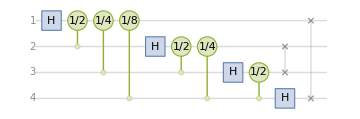

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^((ⅈ π)/4)),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^((ⅈ π)/8))}

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | (-1)^(1/8) | (-1)^(1/4) | (-1)^(3/8) | ⅈ | (-1)^(5/8) | (-1)^(3/4) | (-1)^(7/8) | -1 | -(-1)^(1/8) | -(-1)^(1/4) | -(-1)^(3/8) | -ⅈ | -(-1)^(5/8) | -(-1)^(3/4) | -(-1)^(7/8)
1 | (-1)^(1/4) | ⅈ | (-1)^(3/4) | -1 | -(-1)^(1/4) | -ⅈ | -(-1)^(3/4) | 1 | (-1)^(1/4) | ⅈ | (-1)^(3/4) | -1 | -(-1)^(1/4) | -ⅈ | -(-1)^(3/4)
1 | (-1)^(3/8) | (-1)^(3/4) | -(-1)^(1/8) | -ⅈ | -(-1)^(7/8) | (-1)^(1/4) | (-1)^(5/8) | -1 | -(-1)^(3/8) | -(-1)^(3/4) | (-1)^(1/8) | ⅈ | (-1)^(7/8) | -(-1)^(1/4) | -(-1)^(5/8)
1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ
1 | (-1)^(5/8) | -(-1)^(1/4) | -(-1)^(7/8) | ⅈ | -(-1)^(1/8) | -(-1)^(3/4) | (-1)^(3/8) | -1 | -(-1)^(5/8) | (-1)^(1/4) | (-1)^(7/8) | -ⅈ | (-1)^(1/8) | (-1)^(3/4) | -(-1)^(3/8)
1 | (-1)^(3/4) | -ⅈ | (-1)^(1/4) | -1 | -(-1)^(3/4) | ⅈ | -(-1)^(1/4) | 1 | (-1)^(3/4) | -ⅈ | (-1)^(1/4) | -1 | -(-1)^(3/4) | ⅈ | -(-1)^(1/4)
1 | (-1)^(7/8) | -(-1)^(3/4) | (-1)^(5/8) | -ⅈ | (-1)^(3/8) | -(-1)^(1/4) | (-1)^(1/8) | -1 | -(-1)^(7/8) | (-1)^(3/4) | -(-1)^(5/8) | ⅈ | -(-1)^(3/8) | (-1)^(1/4) | -(-1)^(1/8)
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | -(-1)^(1/8) | (-1)^(1/4) | -(-1)^(3/8) | ⅈ | -(-1)^(5/8) | (-1)^(3/4) | -(-1)^(7/8) | -1 | (-1)^(1/8) | -(-1)^(1/4) | (-1)^(3/8) | -ⅈ | (-1)^(5/8) | -(-1)^(3/4) | (-1)^(7/8)
1 | -(-1)^(1/4) | ⅈ | -(-1)^(3/4) | -1 | (-1)^(1/4) | -ⅈ | (-1)^(3/4) | 1 | -(-1)^(1/4) | ⅈ | -(-1)^(3/4) | -1 | (-1)^(1/4) | -ⅈ | (-1)^(3/4)
1 | -(-1)^(3/8) | (-1)^(3/4) | (-1)^(1/8) | -ⅈ | (-1)^(7/8) | (-1)^(1/4) | -(-1)^(5/8) | -1 | (-1)^(3/8) | -(-1)^(3/4) | -(-1)^(1/8) | ⅈ | -(-1)^(7/8) | -(-1)^(1/4) | (-1)^(5/8)
1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ
1 | -(-1)^(5/8) | -(-1)^(1/4) | (-1)^(7/8) | ⅈ | (-1)^(1/8) | -(-1)^(3/4) | -(-1)^(3/8) | -1 | (-1)^(5/8) | (-1)^(1/4) | -(-1)^(7/8) | -ⅈ | -(-1)^(1/8) | (-1)^(3/4) | (-1)^(3/8)
1 | -(-1)^(3/4) | -ⅈ | -(-1)^(1/4) | -1 | (-1)^(3/4) | ⅈ | (-1)^(1/4) | 1 | -(-1)^(3/4) | -ⅈ | -(-1)^(1/4) | -1 | (-1)^(3/4) | ⅈ | (-1)^(1/4)
1 | -(-1)^(7/8) | -(-1)^(3/4) | -(-1)^(5/8) | -ⅈ | -(-1)^(3/8) | -(-1)^(1/4) | -(-1)^(1/8) | -1 | (-1)^(7/8) | (-1)^(3/4) | (-1)^(5/8) | ⅈ | (-1)^(3/8) | (-1)^(1/4) | (-1)^(1/8))

```mathematica
qft4=QuantumCircuitOperator[{"Fourier",4}];
%["Diagram"](*最后交换高低位约定*)
(#["Matrix"]//Normal//MatrixForm)&/@(qft4["Operators"][[2;;4]])(*qft4的第二到到第四个算符*)
4 qft4["Matrix"]//Normal//FullSimplify//MatrixForm
```

```mathematica
ω=E^((2π I)/2^4);
Table[ω^(i j),{i,0,15},{j,0,15}] //Normal//FullSimplify//MatrixForm(*根据前述公式*)
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | (-1)^(1/8) | (-1)^(1/4) | (-1)^(3/8) | ⅈ | (-1)^(5/8) | (-1)^(3/4) | (-1)^(7/8) | -1 | -(-1)^(1/8) | -(-1)^(1/4) | -(-1)^(3/8) | -ⅈ | -(-1)^(5/8) | -(-1)^(3/4) | -(-1)^(7/8)
1 | (-1)^(1/4) | ⅈ | (-1)^(3/4) | -1 | -(-1)^(1/4) | -ⅈ | -(-1)^(3/4) | 1 | (-1)^(1/4) | ⅈ | (-1)^(3/4) | -1 | -(-1)^(1/4) | -ⅈ | -(-1)^(3/4)
1 | (-1)^(3/8) | (-1)^(3/4) | -(-1)^(1/8) | -ⅈ | -(-1)^(7/8) | (-1)^(1/4) | (-1)^(5/8) | -1 | -(-1)^(3/8) | -(-1)^(3/4) | (-1)^(1/8) | ⅈ | (-1)^(7/8) | -(-1)^(1/4) | -(-1)^(5/8)
1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ
1 | (-1)^(5/8) | -(-1)^(1/4) | -(-1)^(7/8) | ⅈ | -(-1)^(1/8) | -(-1)^(3/4) | (-1)^(3/8) | -1 | -(-1)^(5/8) | (-1)^(1/4) | (-1)^(7/8) | -ⅈ | (-1)^(1/8) | (-1)^(3/4) | -(-1)^(3/8)
1 | (-1)^(3/4) | -ⅈ | (-1)^(1/4) | -1 | -(-1)^(3/4) | ⅈ | -(-1)^(1/4) | 1 | (-1)^(3/4) | -ⅈ | (-1)^(1/4) | -1 | -(-1)^(3/4) | ⅈ | -(-1)^(1/4)
1 | (-1)^(7/8) | -(-1)^(3/4) | (-1)^(5/8) | -ⅈ | (-1)^(3/8) | -(-1)^(1/4) | (-1)^(1/8) | -1 | -(-1)^(7/8) | (-1)^(3/4) | -(-1)^(5/8) | ⅈ | -(-1)^(3/8) | (-1)^(1/4) | -(-1)^(1/8)
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | -(-1)^(1/8) | (-1)^(1/4) | -(-1)^(3/8) | ⅈ | -(-1)^(5/8) | (-1)^(3/4) | -(-1)^(7/8) | -1 | (-1)^(1/8) | -(-1)^(1/4) | (-1)^(3/8) | -ⅈ | (-1)^(5/8) | -(-1)^(3/4) | (-1)^(7/8)
1 | -(-1)^(1/4) | ⅈ | -(-1)^(3/4) | -1 | (-1)^(1/4) | -ⅈ | (-1)^(3/4) | 1 | -(-1)^(1/4) | ⅈ | -(-1)^(3/4) | -1 | (-1)^(1/4) | -ⅈ | (-1)^(3/4)
1 | -(-1)^(3/8) | (-1)^(3/4) | (-1)^(1/8) | -ⅈ | (-1)^(7/8) | (-1)^(1/4) | -(-1)^(5/8) | -1 | (-1)^(3/8) | -(-1)^(3/4) | -(-1)^(1/8) | ⅈ | -(-1)^(7/8) | -(-1)^(1/4) | (-1)^(5/8)
1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ
1 | -(-1)^(5/8) | -(-1)^(1/4) | (-1)^(7/8) | ⅈ | (-1)^(1/8) | -(-1)^(3/4) | -(-1)^(3/8) | -1 | (-1)^(5/8) | (-1)^(1/4) | -(-1)^(7/8) | -ⅈ | -(-1)^(1/8) | (-1)^(3/4) | (-1)^(3/8)
1 | -(-1)^(3/4) | -ⅈ | -(-1)^(1/4) | -1 | (-1)^(3/4) | ⅈ | (-1)^(1/4) | 1 | -(-1)^(3/4) | -ⅈ | -(-1)^(1/4) | -1 | (-1)^(3/4) | ⅈ | (-1)^(1/4)
1 | -(-1)^(7/8) | -(-1)^(3/4) | -(-1)^(5/8) | -ⅈ | -(-1)^(3/8) | -(-1)^(1/4) | -(-1)^(1/8) | -1 | (-1)^(7/8) | (-1)^(3/4) | (-1)^(5/8) | ⅈ | (-1)^(3/8) | (-1)^(1/4) | (-1)^(1/8))

```mathematica
qft4[1/(√2)QuantumState["0001"]+1/(√2)QuantumState["0011"]]["Matrix"]//Normal//Flatten//N;
SparseArray[{2->1/(√2),4->1/(√2)},16]//Fourier;
%-%%//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### n比特：一般情况的分析

检验：下面的电路除了高低位相反以外，实现了Fourier变换

-Graphics-

-Graphics-

-Graphics-

## QFT的应用：相位估计

-Graphics-

#### 例：单比特的幺正算符的相位估计

```mathematica
ϕ=1./4+1/8;(*完美的二进制数*)
%//Rationalize
BaseForm[ϕ,2]
u=QuantumOperator[{"Phase",2π Rationalize@ϕ}];
%//TraditionalForm//Chop
```

3/8

0.011_2

00+ⅇ^((3 ⅈ π)/4)11

```mathematica
Eigensystem[u["Matrix"]]//ComplexExpand(*本征值和本征态*)
AbsArg[%[[1,2]]](*相位和幅角*)
```

{{1,-(1-ⅈ)/(√2)},{{1,0},{0,1}}}

{1,(3 π)/4}

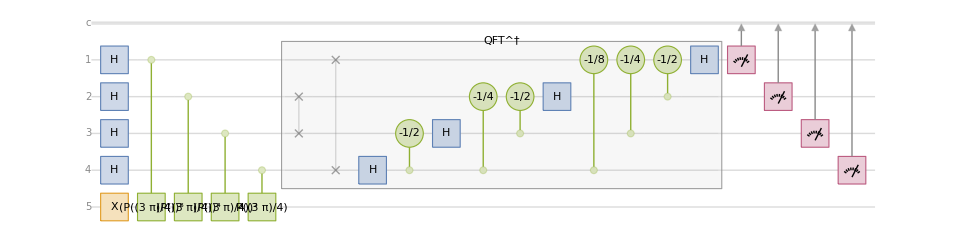

```mathematica
pe=QuantumCircuitOperator[{"PhaseEstimation",u,4}];
%["Diagram"](*第一个寄存器制备均匀叠加态，第二个寄存器制备U本征态，作用CU^k 若干次，做反傅里叶变换，测量第一个寄存器*)
```

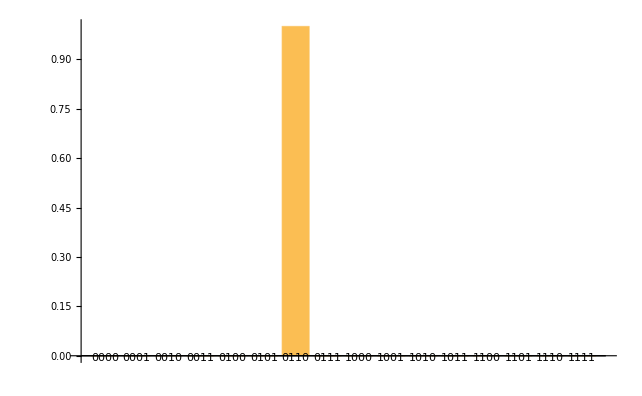

```mathematica
pe[QuantumState["00000"]]["ProbabilityPlot"]
```

```mathematica
ϕ=1./4+1/8+0.02;(*不完美的二进制数，即无限小数*)
BaseForm[ϕ,2]
u=QuantumOperator[{"Phase",2π ϕ}];
%//TraditionalForm//Chop
```

0.011001010001111010111_2

00+(-0.790155+0.612907 ⅈ)11

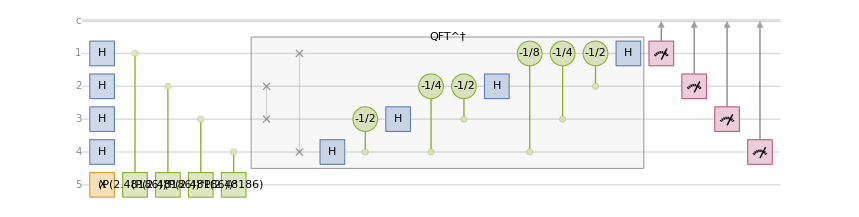

```mathematica
pe=QuantumCircuitOperator[{"PhaseEstimation",u,4}];
%["Diagram"]
```

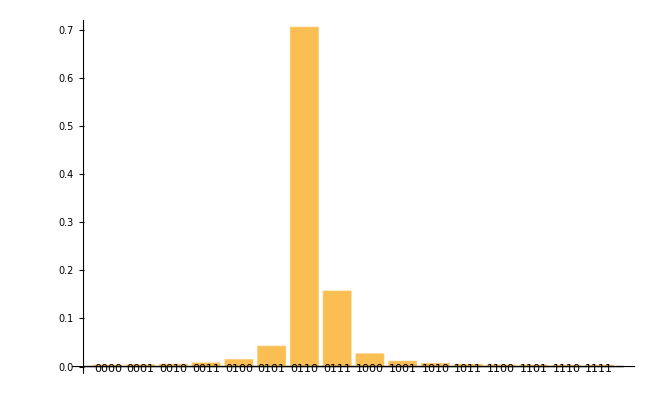

```mathematica
pe[QuantumState["00000"]]["ProbabilityPlot"]
```

#### 一般情况的分析(相位是完美的二进制小数)

-Graphics-

二进制小数乘二，小数点向右跳一位

为什么mma的线路与书上的黑盒的作用的顺序是相反的？相当于SWAP被移动到了线路最左边，然后就不需要SWAP了

回顾：正Fourier变换

## 加法器

## 大数分解与Shor算法

### 大数分解问题与RSA加密

Shor 算法解决大数分解问题。大数分解的困难性保证了 RSA (Rivest-Shamir-Adleman) 公钥密码通信的安全性。通用数域筛 (GNFS) 是已知用于分解大于 10^100 的整数的最高效的经典5算法。

分解整数n ( 表示整数 n 仅需 [log_2 n]+1个比特 ) 的GNFS 计算步数

RSA 分解挑战

-Graphics-

京东价格：7999

量子计算机的实用化标志：RSA数中任意一个的分解。(2045)

### Shor算法主要步骤

-Graphics-

-Graphics-

## 量子傅里叶变换的一般应用

## 参考文献和注释

1	Quantum algorithms:
A survey of applications and end-to-end complexities

2	文中所说的“端到端”是指解决用户感兴趣的整个问题的成本，而不仅仅是运行作为完整解决方案子程序的特定量子电路的成本。

3	Quantum algorithms:
A survey of applications and end-to-end complexities

4	Quantum algorithms:
A survey of applications and end-to-end complexities

5	确定性?